```mathematica
M={{1,2,3},{1,2,3},{7,8,9}}
ID= IdentityMatrix[3]
```

{{1,2,3},{1,2,3},{7,8,9}}

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
orthoChain[Q0_, m_, L_]:= Module[{dummyP, theta, Eij, l,K, sign},
If [OrthogonalMatrixQ[Q0]==False,Print["Initial matrix is NOT orthogonal."]; Return[Q0//MatrixForm], Nothing];
dummyP = Q0;
Table[
theta = RandomReal[{0,2*Pi}]; 
{i,j}=RandomSample[Range[1,m],2]  ;
Eij = IdentityMatrix[m];
Eij[[i,i]] = Cos[theta];
Eij[[j,j]] =  Cos[theta];
Eij[[i,j]] = Sin[theta];
Eij[[j,i]] = -Sin[theta];
{l} = RandomSample[{i,j},1];
{sign}= RandomSample[{-1,1},1];
sign*Eij[[l,;;]];
dummyP = Eij.dummyP;
dummyP
,{ii, 1, L}]
]
```

```mathematica
Map[MatrixForm,orthoChain[ID,3, 5]]
```

{(0.632474 | 0. | 0.774581
0. | 1. | 0.
-0.774581 | 0. | 0.632474),(0.632474 | 0. | 0.774581
0.0659057 | -0.996374 | -0.0538145
0.771772 | 0.0850856 | -0.630181),(0.632474 | 0. | 0.774581
-0.649244 | 0.545382 | 0.530132
-0.422443 | -0.838187 | 0.34494),(0.632474 | 0. | 0.774581
0.461988 | 0.802661 | -0.377231
-0.621726 | 0.596436 | 0.507662),(-0.561365 | -0.0646427 | -0.82504
0.461988 | 0.802661 | -0.377231
0.686612 | -0.592923 | -0.420721)}

```mathematica
orthoChain2[Q0_, m_, L_]:= Module[{dummyP, Eij, l, sign,K},
Clear[theta];
If [OrthogonalMatrixQ[Q0]==False,Print["Initial matrix is NOT orthogonal."]; Return[Q0//MatrixForm], Nothing];
dummyP = Q0;
Table[
{i,j}=RandomSample[Range[1,m],2];
Eij = IdentityMatrix[m];
Eij[[i,i]] = Cos[theta];
Eij[[j,j]] = Cos[theta];
Eij[[i,j]] = Sin[theta];
Eij[[j,i]] = -Sin[theta];
{l} = RandomSample[{i,j},1];
{sign}= RandomSample[{-1,1},1];
sign*Eij[[l,;;]];
dummyP = Eij.dummyP;
dummyP//Tr
,{ii, 1, L}]
]
```

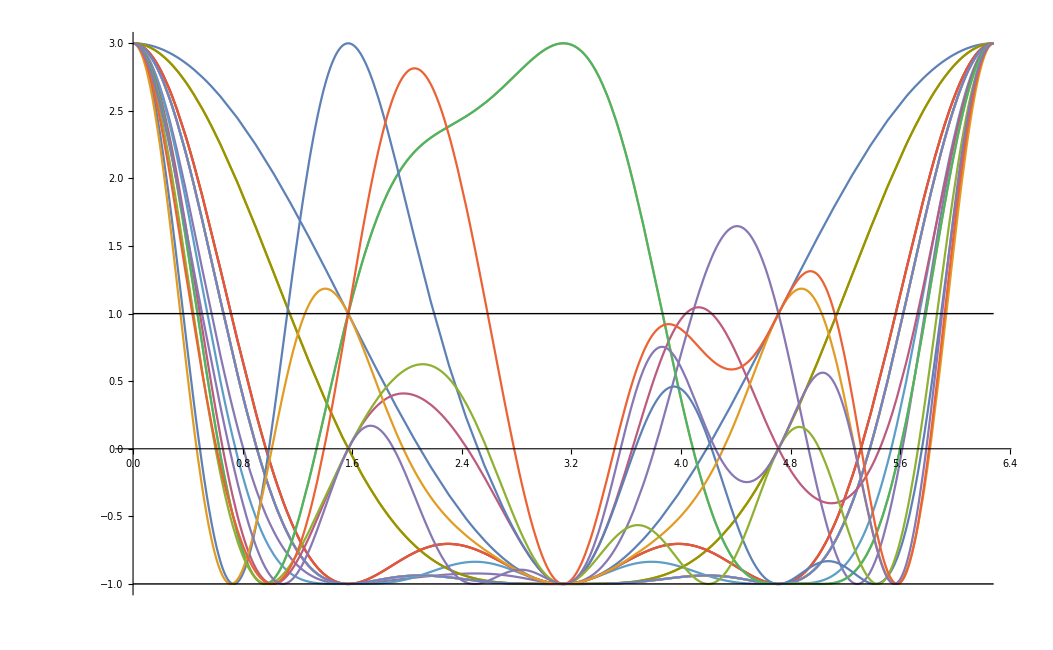

```mathematica
return = orthoChain2[ID, 3, 20];
Plot[return,{theta, 0,2* Pi}, Epilog->{Line[{{0,-1},{2*Pi,-1}}],Line[{{0,1},{2*Pi,1}}]}]
```

```mathematica
return =orthoChain2[ID, 3, 5]; return//TableForm
```

1+2 Cos[theta]
2 Cos[theta]+Cos[theta]^2
Cos[theta]+Cos[theta]^2+Cos[theta]^3-Sin[theta]^2-Cos[theta] Sin[theta]^2
Cos[theta]^2+Cos[theta]^3-Sin[theta]^2+Cos[theta] (Cos[theta]^2-Cos[theta] Sin[theta]^2)
Cos[theta]^2-Sin[theta]^3+Sin[theta] (-Cos[theta] Sin[theta]-Cos[theta]^2 Sin[theta])+Cos[theta] (Cos[theta]^3-Sin[theta]^2)-Sin[theta] (-Cos[theta] Sin[theta]^2+Cos[theta] (Cos[theta] Sin[theta]+Cos[theta]^2 Sin[theta]))+Cos[theta] (Sin[theta]^3+Cos[theta] (Cos[theta]^2-Cos[theta] Sin[theta]^2))

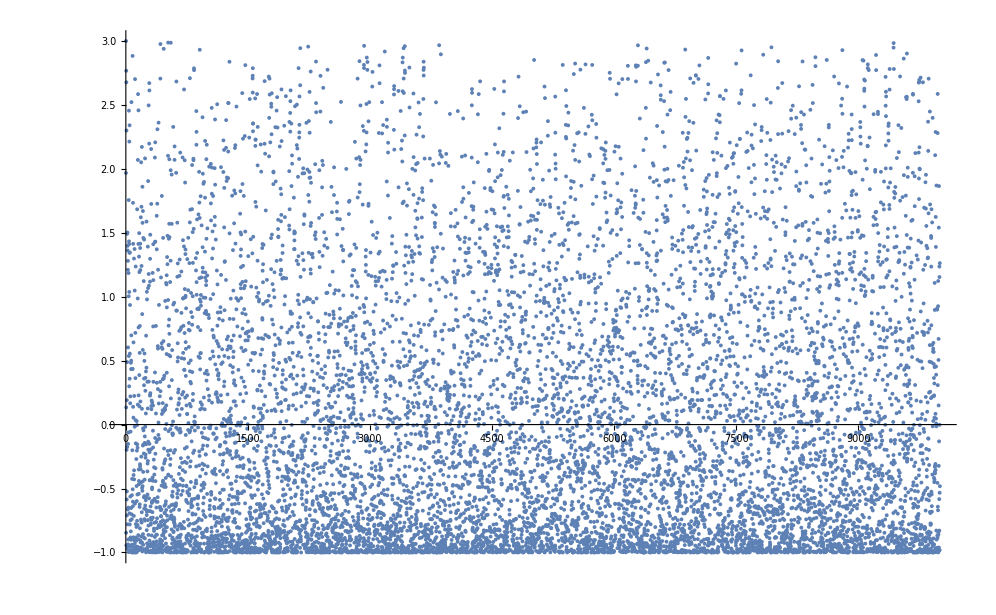

```mathematica
Map[Tr,orthoChain[ID,3, 10000]]//ListPlot
```

```mathematica
simulation =Parallelize[Table[Map[Tr,orthoChain[ID,3, 10000]]//Mean,{1000}]];
```

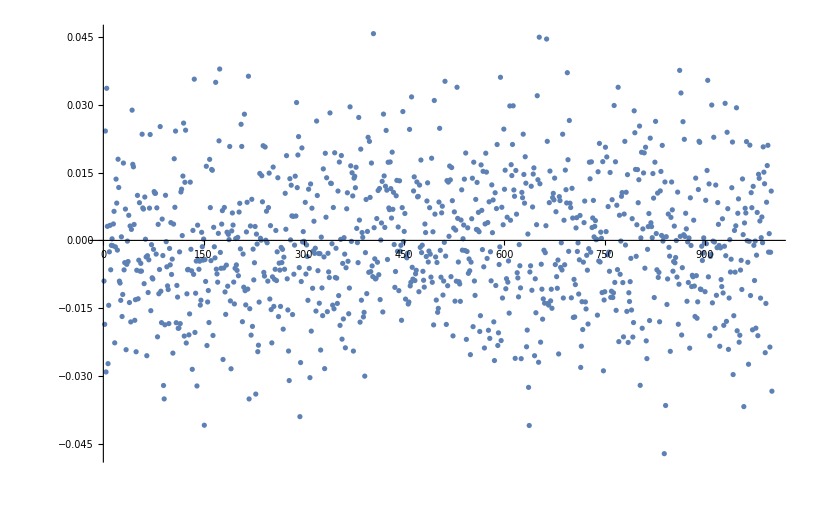

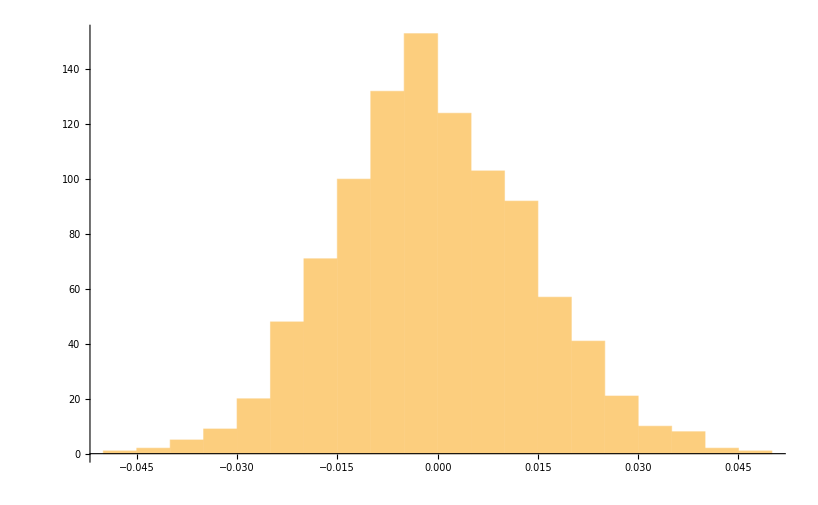

```mathematica
ListPlot[simulation]
Histogram[simulation]
```

```mathematica
ListPointPlot3D[Map[Diagonal,orthoChain[ID,3, 10000]]]
```

-Graphics3D-